```mathematica
A=({{9/10, -3/10, 1}, {-7/5, 4/5, -2}, {-7/5, 3/10, -3/2}})
```

{{9/10,-3/10,1},{-7/5,4/5,-2},{-7/5,3/10,-3/2}}

```mathematica
MatrixForm[A]
```

(9/10 | -3/10 | 1
-7/5 | 4/5 | -2
-7/5 | 3/10 | -3/2)

```mathematica
λ=Eigenvalues[A]
```

{-1/2,1/2,1/5}

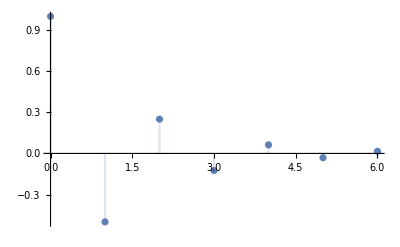

```mathematica
DiscretePlot[λ[[1]]^k,{k,0,6},PlotRange->All]
```

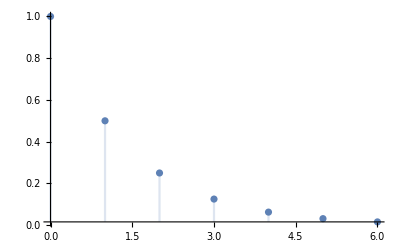

```mathematica
DiscretePlot[λ[[2]]^k,{k,0,6},PlotRange->All]
```

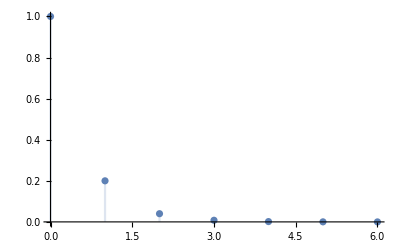

```mathematica
DiscretePlot[λ[[3]]^k,{k,0,6},PlotRange->All]
```

```mathematica
T=Transpose[Eigenvectors[A]]
```

{{-1/2,-1,-1},{1,2,1},{1,1,1}}

```mathematica
MatrixForm[T]
```

(-1/2 | -1 | -1
1 | 2 | 1
1 | 1 | 1)

```mathematica
λ
```

{-1/2,1/2,1/5}

```mathematica
A.T[[All,1]]
```

{1/4,-1/2,-1/2}

```mathematica
A.T[[All,3]]
```

{-1/5,1/5,1/5}

```mathematica
Subscript[x, 0]={{3},{-2},{0}}
```

{{3},{-2},{0}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{6},{-2},{-4}}

```mathematica
{n,n}=Dimensions[A]
```

{3,3}

```mathematica
Subscript[x, l][k_]:=∑_(i=1)^n T[[All,i]] λ[[i]]^k Subscript[z, 0][[i,1]]
```

```mathematica
MatrixForm[Subscript[x, l][k]]
```

(-3 (-1/2)^k+2^(1-k)+4 5^-k
3 (-1)^k 2^(1-k)-2^(2-k)-4 5^-k
-2^(1-k)+3 (-1)^k 2^(1-k)-4 5^-k)

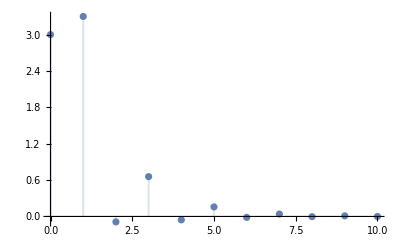

```mathematica
DiscretePlot[Subscript[x, l][k][[1]],{k,0,10},PlotRange->All]
```

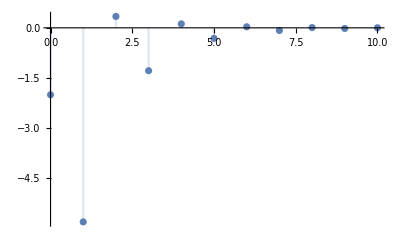

```mathematica
DiscretePlot[Subscript[x, l][k][[2]],{k,0,10},PlotRange->All]
```

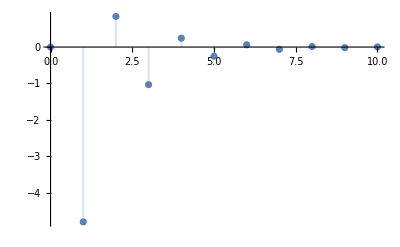

```mathematica
DiscretePlot[Subscript[x, l][k][[3]],{k,0,10},PlotRange->All]
```

```mathematica
Subscript[x, 0]={{2},{-4},{-4}}
```

{{2},{-4},{-4}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{-4},{0},{0}}

```mathematica
Subscript[x, l][k_]:=∑_(i=1)^n T[[All,i]] λ[[i]]^k Subscript[z, 0][[i,1]]
```

```mathematica
MatrixForm[Subscript[x, l][k]]
```

((-1)^k 2^(1-k)
-(-1)^k 2^(2-k)
-(-1)^k 2^(2-k))